```mathematica
Simplify[1-(2*r*b+d)/(2*d-b)+(2*r*b)/d+(2*r*b^2+d*b)/(2*d^2-d*b)]
```

-(d+2 b r)/(b-2 d)

```mathematica
Simplify[-(d+2 *b *r)/(b-2 *d)*(2*d)/(2*d-b)*(2*r*b+d)/(4*b)]
```

(d (d+2 b r)^2)/(2 b (b-2 d)^2)

```mathematica
Simplify[(d *(d+2 *b *r)^2)/(2 *b* (b-2 *d)^2)+l*((b-1-j)/(2*b))-((2*r*b+d)/((2*d-b)*2))^2]
```

-((d^2+4 d ((-1+b-j) l+b r)+2 b ((1-b+j) l+2 b r^2))/(4 b (b-2 d)))

```mathematica
j = -√((1+b)^2-4*r*b)
d = (a-b)*(b-1-j)
```

-√((1+b)^2-4 b r)

(a-b) (-1+b+√((1+b)^2-4 b r))

```mathematica
Manipulate[Plot[-((d^2+4 d ((-1+b-j) l+b r)+2 b ((1-b+j) l+2 b r^2))/(4 b (b-2 d))),{r,-100,100}],{l,0,100},{b,0.1,100},{a,0.1,100}]
```

```mathematica
Simplify[√(1-r)(a-1+√(1-r))+r*Log[1-√(1-r)]]
```

(-1+a+√(1-r)) √(1-r)+r Log[1-√(1-r)]

```mathematica
Manipulate[Plot[√(1-r)(a-1+√(1-r))+r*Log[1-√(1-r)],{r,0,1}],{a,1,10}]
```

```mathematica
Manipulate[Plot[{1/2(((1+a)/a)+√(((1+a)/a)^2-4*r/a)),1/2(((1+a)/a)-√(((1+a)/a)^2-4*r/a))},{r,0,1}],{a,0.01,5}]
```

```mathematica
Manipulate[Plot[{1/2(((1+a)/a)-√(((1+a)/a)^2-4*r/a))},{r,0,1}],{a,0.01,5}]
```

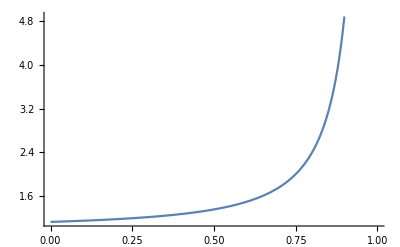

```mathematica
Plot[1+1/(8*(1-r)^(3/2)),{r,0,1}]
```

```mathematica
p*(1-(p-r-k)/m)+l*√(1-r)-k^2
```

```mathematica
Simplify[Solve[{D[p*(1-(p-r-k)/m)+l*(1-(p-r-k)/m)-k^2 ,k]==0,D[p*(1-(p-r-k)/m)+l*(1-(p-r-k)/m)-k^2 ,p]==0 },{k,p}]]
```

{{k→(l+m+r)/(-1+4 m),p→(l-2 l m+2 m (m+r))/(-1+4 m)}}

```mathematica
Simplify[(l-2 l m+2 m (m+r))/(-1+4 m)*(1-((l-2 l m+2 m (m+r))/(-1+4 m)-r-(l+m+r)/(-1+4 m))/m)+l*(1-((l-2 l m+2 m (m+r))/(-1+4 m)-r-(l+m+r)/(-1+4 m))/m)-((l+m+r)/(-1+4 m))^2]
```

(l+m+r)^2/(-1+4 m)

```mathematica
p*(1-(p-r-k)/m)+l*√(1-r)-k^2
```

```mathematica
Simplify[Solve[{D[p*(1-(p-r-k)/m)+l*√(1-r)-k^2 ,k]==0,D[p*(1-(p-r-k)/m)+l*√(1-r)-k^2 ,p]==0 },{k,p}]]
```

{{k→(m+r)/(-1+4 m),p→(2 m (m+r))/(-1+4 m)}}

```mathematica
Simplify[(2 m (m+r))/(-1+4 m)*(1-((2 m (m+r))/(-1+4 m)-r-(m+r)/(-1+4 m))/m)+l*√(1-r)-((m+r)/(-1+4 m))^2]
```

```mathematica
(m^2-l √(1-r)+r^2+2 m (2 l √(1-r)+r))/(-1+4 m)
```

```mathematica
Simplify[Solve[{D[p*(1-(p-r-k)/m)+l*√(1-r)-k^2+g*(p-k-m+a(1-r)-1),k]==0,D[p*(1-(p-r-k)/m)+l*√(1-r)-k^2+g*(p-k-m+a(1-r)-1),p]==0,D[p*(1-(p-r-k)/m)+l*√(1-r)-k^2+g*(p-k-m+a(1-r)-1),g]==0 },{p,k,g}]]
```

{{p→(-1+2 m+2 m^2+a (-1+2 m) (-1+r)+r)/(2 m),k→(-1+a+r-a r)/(2 m),g→(-1+2 m^2-2 m (-2+r)+a (-1+4 m) (-1+r)+r)/(2 m^2)}}

```mathematica
Simplify[(-1+2 m+2 m^2+a (-1+2 m) (-1+r)+r)/(2 m)*(1-((-1+2 m+2 m^2+a (-1+2 m) (-1+r)+r)/(2 m)-r-(-1+a+r-a r)/(2 m))/m)+l*√(1-r)-((-1+a+r-a r)/(2 m))^2]
```

(4 m (-1+r)+(-1+r)^2-a^2 (-1+4 m) (-1+r)^2+4 m^2 (-1+l √(1-r)+r)-2 a (-1+r) (-1+2 m^2-2 m (-2+r)+r))/(4 m^2)

```mathematica
Manipulate[Plot[(-1+2 ((a-1)√(1-r))^2-2 ((a-1)√(1-r))^2 (-2+r)+a (-1+4 ((a-1)√(1-r))^2) (-1+r)+r)/(2 (((a-1)√(1-r))^2)^2),{r,0,1}],{a,1.8,15}]
```

```mathematica
Manipulate[Plot[(((a-1)√(1-r))^2-b* √(1-r)+r^2+2 ((a-1)√(1-r)) (2* b √(1-r)+r))/(-1+4 ((a-1)√(1-r))),{r,0,1}],{a,1.5,10},{b,1,10}]
```

```mathematica
Simplify[Solve[D[(((a-1)√(1-r))^2-l √(1-r)+r^2+2 ((a-1)√(1-r)) (2 l √(1-r)+r))/(-1+4 ((a-1)√(1-r))),r]==0,r]]
```

$Aborted

```mathematica
Manipulate[Plot[2 ((a-1)√(1-r)) (r),{r,0,1}],{a,1.25,20},{l,0,20}]
```

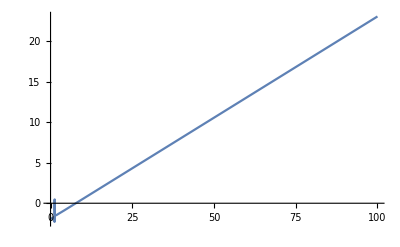

```mathematica
Plot[(a-1)^2/(4a-5)-7/4 ,{a,0,100}]
```

```mathematica
Solve[(a-1)^2/(4a-5)-7/4==0,a]
```

{{a→1/2 (9-√42)},{a→1/2 (9+√42)}}

```mathematica
TeXForm[(((a-1)√(1-r))^2-b* √(1-r)+r^2+2 ((a-1)√(1-r)) (2* b √(1-r)+r))/(-1+4 ((a-1)√(1-r)))]
```

\frac{2 (a-1) \sqrt{1-r} \left(2 b \sqrt{1-r}+r\right)+(a-1)^2 (1-r)-b \sqrt{1-r}+r^2}{4 (a-1) \sqrt{1-r}-1}

```mathematica
Manipulate[Plot3D[(((a-1)√(1-r))^2-b* √(1-r)+r^2+2 ((a-1)√(1-r)) (2* b √(1-r)+r))/(-1+4 ((a-1)√(1-r))),{r,0,1},{a,1.5,10},AxesLabel->{Style[r,FontSize->25],Style[alpha,FontSize->25],Style[profit,FontSize->25]}],{b,1,15}]
```

```mathematica
Plot[Sin[x]^2,{x,0,2 Pi},PlotLabel->Style[StandardForm[Sin[x]^2],FontSize->12]]
```

```mathematica
Manipulate[Plot[(a-1)^2/(4*a-1)-(1/2),{a,1,15}],{r,0,1}]
```

```mathematica
Simplify[(a-1)^2/(4*a-5)-((a-1)√(1-r)-(a-1)(1-r)+3/2+l)*(√(1-r)+a*(1-r))/(1+a*√(1-r))]
```

(-1+a)^2/(-1+4 a)-((3/2+l+(-1+a) √(1-r)+(-1+a) (-1+r)) (a+√(1-r)-a r))/(1+a √(1-r))

```mathematica
Manipulate[Plot[(((a-1)√(1-r))^2-b* √(1-r)+r^2+2 ((a-1)√(1-r)) (2* b √(1-r)+r))/(-1+4 ((a-1)√(1-r)))-((a-1)√(1-r)-(a-1)(1-r)+3/2+b)*(√(1-r)+a*(1-r))/(1+a*√(1-r)),{r,0,1}],{b,0,10},{a,1.8,13}]
```

```mathematica
Simplify[(((a-1)√(1-r))^2-b* √(1-r)+r^2+2 ((a-1)√(1-r)) (2* b √(1-r)+r))/(-1+4 ((a-1)√(1-r)))-((a-1)√(1-r)-(a-1)(1-r)+3/2+b)*(√(1-r)+a*(1-r))/(1+a*√(1-r))]
```

-((3/2+b+(-1+a) √(1-r)+(-1+a) (-1+r)) (a+√(1-r)-a r))/(1+a √(1-r))+(-b √(1-r)-(-1+a)^2 (-1+r)+r^2+2 (-1+a) √(1-r) (2 b √(1-r)+r))/(-1+4 (-1+a) √(1-r))

```mathematica
Solve[(a-1)^2/(4*a-5)-(1/2)== 0,a]
```

{{a→1/2 (4-√2)},{a→1/2 (4+√2)}}

```mathematica
√10
```

√10

```mathematica
N[√10]
```

3.16228

```mathematica
N[√2*.5]
```

0.707107

```mathematica
1/2 (4-√2)
```

1/2 (4-√2)

```mathematica
N[1/2 (4-√2)]
```

1.29289

```mathematica
1/2 (4+√2)
```

1/2 (4+√2)

```mathematica
N[1/2 (4+√2)]
```

2.70711

```mathematica
Solve[-((3/2+b+(-1+a) √(1-r)+(-1+a) (-1+r)) (a+√(1-r)-a r))/(1+a √(1-r))+(-b √(1-r)-(-1+a)^2 (-1+r)+r^2+2 (-1+a) √(1-r) (2 b √(1-r)+r))/(-1+4 (-1+a) √(1-r))==0,a]
```

```mathematica
Solve[Simplify[(((a-1)√(1-r))^2-b* √(1-r)+r^2+2 ((a-1)√(1-r)) (2* b √(1-r)+r))/(-1+4 ((a-1)√(1-r)))-((a-1)√(1-r)-(a-1)(1-r)+3/2+b)*(√(1-r)+a*(1-r))/(1+a*√(1-r)),a== 2.3]==0,r]
```

{{r→-1.8279},{r→0.679303}}

```mathematica
Solve[Simplify[(((a-1)√(1-r))^2-b* √(1-r)+r^2+2 ((a-1)√(1-r)) (2* b √(1-r)+r))/(-1+4 ((a-1)√(1-r)))-((a-1)√(1-r)-(a-1)(1-r)+3/2+b)*(√(1-r)+a*(1-r))/(1+a*√(1-r)),a== 1.5]==0,r]
```

{{r→-2.78013},{r→0.417629}}

```mathematica
(p-r-k)Log[p-r-k]== 1+Log[m]
```

```mathematica
1-(p-r-k)Log[p-r-k]== 2k+Log[m]
```

```mathematica
Solve[{(p-r-k)Log[p-r-k]== 1+Log[m],1-(p-r-k)Log[p-r-k]== 2k+Log[m]},p,k]
```

Solve::bdomv: Warning: k is not a valid domain specification. Assuming it is a variable to eliminate.

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{(-k+p-r) Log[-k+p-r]==1+Log[m],1-(-k+p-r) Log[-k+p-r]==2 k+Log[m]},p,k]

```mathematica
Simplify[D[D[k+(a-1)√(1-r)-p+1-k*Log[(p-r-k)/((a-1)√(1-r))]+p*Log[(p-r-k)/((a-1)√(1-r))]-r*Log[(p-r-k)/((a-1)(1-r))]+p*(((a-1)√(1-r)-p+r+k)/((a-1)√(1-r)))+o*√((a-1)√(1-r))-k^2,r],a]]
```

-1/(8 (-1+a)^3 (-1+r)^2)(4 (-p^2+p (2+k-r)-a^2 (-1+r)+2 a (1+√(1-r)) (-1+r)-(1+2 √(1-r)) (-1+r)) √((-1+a) √(1-r))-(-1+a)^2 o (-1+r)) √((-1+a) √(1-r))

```mathematica
Manipulate[Plot[-1/(8 (-1+a)^3 (-1+r)^2)(4 (-p^2+p (2+k-r)-a^2 (-1+r)+2 a (1+√(1-r)) (-1+r)-(1+2 √(1-r)) (-1+r)) √((-1+a) √(1-r))-(-1+a)^2 o (-1+r)) √((-1+a) √(1-r)),{r,0,1}],{p,0,10},{a,1.001,13},{o,0,13},{k,0,10}]
```

```mathematica
Manipulate[Plot[k+(a-1)√(1-r)-p+1-k*Log[(p-r-k)/((a-1)√(1-r))]+p*Log[(p-r-k)/((a-1)√(1-r))]-r*Log[(p-r-k)/((a-1)(1-r))]+p*(((a-1)√(1-r)-p+r+k)/((a-1)√(1-r)))-k^2+o*√(1-r),{r,0,1}],{k,0,1},{a,1.25,5},{p,0,2},{o,0,2}]
```

```mathematica
Solve[D[k+(a-1)√(1-r)-p+1-k*Log[p-r-k]+k*Log[1/((a-1)√(1-r))]+p*Log[p-r-k]-p*Log[1/((a-1)√(1-r))]-r*Log[p-r-k]+r*Log[1/((a-1)(1-r))]+p*(((a-1)√(1-r)-p+r+k)/((a-1)√(1-r)))-k^2+o*√(1-r),k]==0,k]
```

Solve::bdomv: Warning: p is not a valid domain specification. Assuming it is a variable to eliminate.

{{}}

```mathematica
Solve[{D[k+(a-1)√(1-r)-p+1-k*Log[p-r-k]+k*Log[1/((a-1)√(1-r))]+p*Log[p-r-k]-p*Log[1/((a-1)√(1-r))]-r*Log[p-r-k]+r*Log[1/((a-1)(1-r))]+p*(((a-1)√(1-r)-p+r+k)/((a-1)√(1-r)))-k^2+o*√(1-r),p]==0,D[k+(a-1)√(1-r)-p+1-k*Log[p-r-k]+k*Log[1/((a-1)√(1-r))]+p*Log[p-r-k]-p*Log[1/((a-1)√(1-r))]-r*Log[p-r-k]+r*Log[1/((a-1)(1-r))]+p*(((a-1)√(1-r)-p+r+k)/((a-1)√(1-r)))-k^2+o*√(1-r),k]==0},{p,k}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{-1-p/((-1+a) √(1-r))-k/(-k+p-r)+p/(-k+p-r)-r/(-k+p-r)+(k-p+(-1+a) √(1-r)+r)/((-1+a) √(1-r))-Log[1/((-1+a) √(1-r))]+Log[-k+p-r]==0,1-2 k+p/((-1+a) √(1-r))+k/(-k+p-r)-p/(-k+p-r)+r/(-k+p-r)+Log[1/((-1+a) √(1-r))]-Log[-k+p-r]==0},{p,k}]

```mathematica
D[k+(a-1)√(1-r)-p+1-k*Log[p-r-k]+k*Log[1/((a-1)√(1-r))]+p*Log[p-r-k]-p*Log[1/((a-1)√(1-r))]-r*Log[p-r-k]+r*Log[1/((a-1)(1-r))]+p*(((a-1)√(1-r)-p+r+k)/((a-1)√(1-r)))-k^2+o*√(1-r),r]
```

```mathematica
p(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2
```

-k^2+o (1+1/2 (-(1+a)/a-√(((1+a)^2/a+4 k-4 p)/a)))+(1+1/2 (-(1+a)/a-√(((1+a)^2/a+4 k-4 p)/a))) p

```mathematica
Simplify[Solve[{D[p(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2,p]==0,D[p(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2,k]==0},{p,k}]]
```

$Aborted

```mathematica
D[p(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2]
```

```mathematica
Simplify[1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2==0]
```

1/a+√((1+a^2+a (2+4 k-4 p))/a^2)==1

```mathematica
Simplify[1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2==1]
```

1+1/a+√((1+a^2+a (2+4 k-4 p))/a^2)==0

```mathematica
Solve[{D[p*(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2+m*(1+1/a+√((1+a^2+a (2+4 k-4 p))/a^2)),p]==0,D[p*(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2+m*(1+1/a+√((1+a^2+a (2+4 k-4 p))/a^2)),k]==0,D[p*(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2+m*(1+1/a+√((1+a^2+a (2+4 k-4 p))/a^2)),m]==0},{k,m,p}]
```

{{k→1/2,m→1/4 (-1-2 a+2 o),p→1/2}}

```mathematica
Simplify[1/2(1-((1+a)/a+√(1/a*((1+a)^2/a)))/2)+o*(1-((1+a)/a+√(1/a*((1+a)^2/a)))/2)-(1/2)^2]
```

-(1+2 o+a (√((1+a)^2/a^2)+2 (-1+√((1+a)^2/a^2)) o))/(4 a)

```mathematica
Manipulate[Plot[-(1+2 o+a (√((1+a)^2/a^2)+2 (-1+√((1+a)^2/a^2)) o))/(4 a),{a,1,8}],{o,0,100}]
```

```mathematica
Solve[{D[p(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2+m*(1+1/a-√((1+a^2+a (2+4 k-4 p))/a^2)),p]==0,D[p(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2+m*(1+1/a-√((1+a^2+a (2+4 k-4 p))/a^2)),k]==0,D[p(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2+m*(1+1/a-√((1+a^2+a (2+4 k-4 p))/a^2)),m]==0},{k,m,p}]
```

{{k→1/2,m→1/4 (-1-2 a+2 o),p→1/2}}

```mathematica
Manipulate[Plot[1/2*(1-((1+a)/a-√(1/a*((1+a)^2/a)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a)))/2)-(1/2)^2,{a,1,8}],{o,0,5}]
```

```mathematica
Simplify[D[1/2*(1-((1+a)/a-√(1/a*((1+a)^2/a)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a)))/2)-(1/2)^2,a]== 0]
```

```mathematica
Simplify[1/2*(1-((1+a)/a-√(1/a*((1+a)^2/a)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a)))/2)-(1/2)^2]
```

(-1-2 o+a (√((1+a)^2/a^2)+2 (1+√((1+a)^2/a^2)) o))/(4 a)

```mathematica
Solve[{D[p(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2+m*(1+1/a-√((1+a^2+a (2+4 k-4 p))/a^2)),p]==0,D[p(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2+m*(1+1/a-√((1+a^2+a (2+4 k-4 p))/a^2)),k]==0,D[p(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2+m*(1+1/a-√((1+a^2+a (2+4 k-4 p))/a^2)),m]==0},{k,m,p}]
```

{{k→1/2,m→1/4 (-1-2 a+2 o),p→1/2}}

```mathematica
Solve[{D[p(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2,p]==0,k==0},{k,p}]
```

{{k→0,p→(1+4 a+a^2-3 a o-√(1-a-a^3+a^4+3 a o-6 a^2 o+3 a^3 o))/(9 a)},{k→0,p→(1+4 a+a^2-3 a o+√(1-a-a^3+a^4+3 a o-6 a^2 o+3 a^3 o))/(9 a)}}

```mathematica
(1+4 a+a^2-3 a o+√(1-a-a^3+a^4+3 a o-6 a^2 o+3 a^3 o))/(9 a)
```

(1+4 a+a^2-3 a o+√(1-a-a^3+a^4+3 a o-6 a^2 o+3 a^3 o))/(9 a)

```mathematica
Manipulate[Plot3D[{(1+4 a+a^2-3 a o+√(1-a-a^3+a^4+3 a o-6 a^2 o+3 a^3 o))/(9 a),(-1+2 *(a-1)*√(1-r)+2 ((a-1)*√(1-r))^2+a (-1+2 (a-1)*√(1-r)) (-1+r)+r)/(2 (a-1)*√(1-r))},{a,1,8},{o,0,8}],{r,0,1}]
```

```mathematica
Simplify[(1+4 a+a^2-3 a o+√(1-a-a^3+a^4+3 a o-6 a^2 o+3 a^3 o))/(9 a)*(1-((1+a)/a-√(1/a*((1+a)^2/a-4*(1+4 a+a^2-3 a o+√(1-a-a^3+a^4+3 a o-6 a^2 o+3 a^3 o))/(9 a))))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a-4(1+4 a+a^2-3 a o+√(1-a-a^3+a^4+3 a o-6 a^2 o+3 a^3 o))/(9 a))))/2)]
```

((1+a^2+a (4+6 o)+√((-1+a)^2 (1+a+a^2+3 a o))) (-3+a (3+√((5+2 a+5 a^2+12 a o-4 √((-1+a)^2 (1+a+a^2+3 a o)))/a^2))))/(54 a^2)

```mathematica
Solve[{D[p(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2,p]==0,D[p(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2,k]==0},{k,p}]
```

$Aborted

```mathematica
Manipulate[Plot[p*(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2,{a,1.1,4},PlotRange->{0,3}],{k,0,2},{p,0,2}]
```

```mathematica
Manipulate[Plot[{p *(1-1/2 ((1+a)/a-√(((1+a)^2/a-4 p+4 k)/a)))+o (1-1/2 ((1+a)/a-√(((1+a)^2/a-4 p+4 k)/a)))-k^2,p *(1-1/2 ((1+a)/a-√(((1+a)^2/a-4 p+4 (k+.1))/a)))+o (1-1/2 ((1+a)/a-√(((1+a)^2/a-4 p+4 (k+.1))/a)))-(k+.1)^2},{a,1.1,4},PlotRange->{0,3}],{k,0,.9},{p,0,2},{o,0,2}]
```

```mathematica
Solve[D[p(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4*.5)))/2)+o*(1-((1+a)/a-√(1/a*((1+a)^2/a-4p+4*.5)))/2)-(.5)^2,p]==0,p]
```

{{p→0.0277778 (28.+4./a+4. a-12. o-(1. √(16.+8. a-48. a^2+8. a^3+16. a^4+48. a o-96. a^2 o+48. a^3 o))/a)},{p→0.0277778 (28.+4./a+4. a-12. o+(√(16.+8. a-48. a^2+8. a^3+16. a^4+48. a o-96. a^2 o+48. a^3 o))/a)}}

```mathematica
Plot3D[{0.027777777777777776 (28.+4./a+4. a-12. o-(1. √(16.+8. a-48. a^2+8. a^3+16. a^4+48. a o-96. a^2 o+48. a^3 o))/a),0.027777777777777776 (28.+4./a+4. a-12. o+(√(16.+8. a-48. a^2+8. a^3+16. a^4+48. a o-96. a^2 o+48. a^3 o))/a)},{a,1,4},{o,0,6}, PlotRange->{0,1.7}]
```

-Graphics3D-

```mathematica
Plot3D[{0.027777777777777776 (28.+4./a+4. a-12. o-(1. √(16.+8. a-48. a^2+8. a^3+16. a^4+48. a o-96. a^2 o+48. a^3 o))/a)(1-1/2((1+a)/a-√(1/a*((1+a)^2/a-40.027777777777777776 (28.+4./a+4. a-12. o-(1. √(16.+8. a-48. a^2+8. a^3+16. a^4+48. a o-96. a^2 o+48. a^3 o))/a)+4*.5))))+o*(1-1/2((1+a)/a-√(1/a*((1+a)^2/a-40.027777777777777776 (28.+4./a+4. a-12. o-(1. √(16.+8. a-48. a^2+8. a^3+16. a^4+48. a o-96. a^2 o+48. a^3 o))/a)+4*.5))))-(.5)^2,0.027777777777777776 (28.+4./a+4. a-12. o+(√(16.+8. a-48. a^2+8. a^3+16. a^4+48. a o-96. a^2 o+48. a^3 o))/a)(1-1/2((1+a)/a-√(1/a*((1+a)^2/a-40.027777777777777776 (28.+4./a+4. a-12. o+(√(16.+8. a-48. a^2+8. a^3+16. a^4+48. a o-96. a^2 o+48. a^3 o))/a)+4*.5))))+o*(1-1/2((1+a)/a-√(1/a*((1+a)^2/a-40.027777777777777776 (28.+4./a+4. a-12. o+(√(16.+8. a-48. a^2+8. a^3+16. a^4+48. a o-96. a^2 o+48. a^3 o))/a)+4*.5))))-(.5)^2},{a,1,4},{o,0,6}]
```

-Graphics3D-